```mathematica
n=1000; m=1;
```

```mathematica
(*Este código debería calcular el número de ccs, el tamaño de las mismas, la distribución de grados, el GCC, el MCC y la Asortatividad*)kaux={};kaux={};Do[kaux={}; colors={}; {spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0011.txt"]]]; While[spression≠ {0,0, 0}, {kaux=Join[kaux, {spression}],  spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0011.txt"]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], colors=Table[kaux[[i,3]], {i,1,Length[kaux]}]} , m];
```

```mathematica
vect={}; Do[{If[colors[[i]]==1,vect=Join[vect, {{1,0,0}}]], If[colors[[i]]==0,vect=Join[vect, {{0,1,0}}]]}, {i,1,Length[colors]}]
```

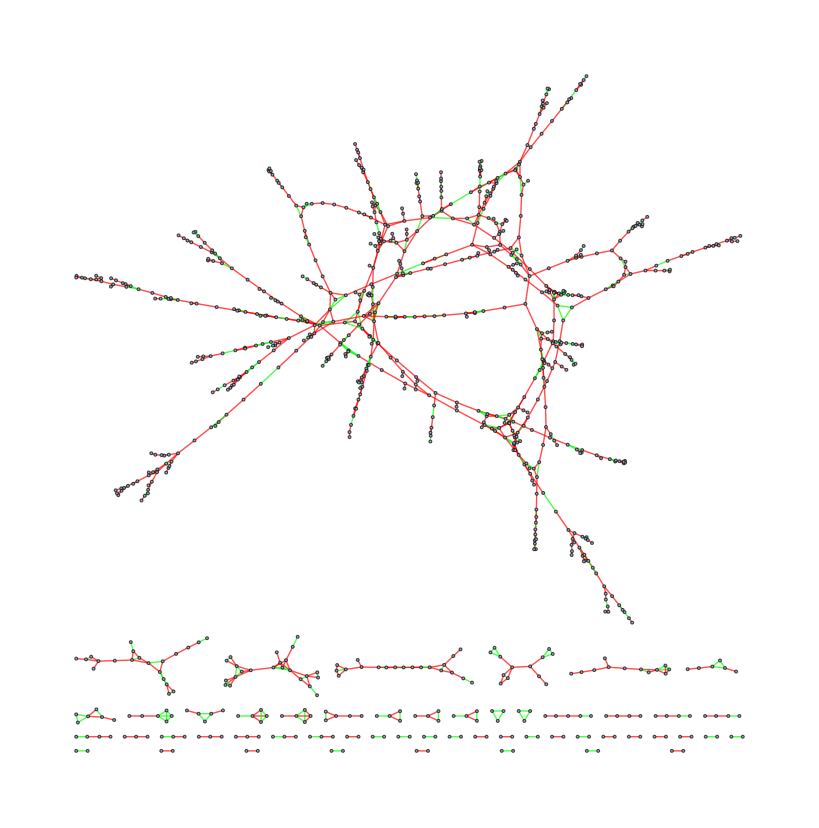

```mathematica
Graph[t, EdgeStyle->Flatten[Table[t[[i]]->RGBColor[vect[[i]]], {i, 1, Length[t]}]]]
```